```mathematica
sumIntDigits[n_, b_]:=Total[IntegerDigits[n, b]]
```

```mathematica
sumIntDigits[17, 10]
```

8

```mathematica
sumIntDigits[10, 2]
```

2

```mathematica
expSumList[n_ ,b_, p_]:=Accumulate[Exp[2.0*Pi*I*sumIntDigits[#, b]/p]&/@Range[n]]
```

```mathematica
Range[4.23123]
```

{1,2,3,4}

```mathematica
expSumList[1000,10, 4];
```

```mathematica
visualizer[n_, b_, p_]:=ListLinePlot[ReIm /@ expSumList[n,b, p]]
```

```mathematica
visualizer[10000000, 2, 4]
```

-Graphics-

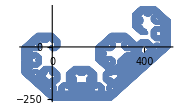

```mathematica
Show[%,ImageSize->Small]
```

```mathematica
(* Table of some integer visualizations in base 10, varying by param p *)
```

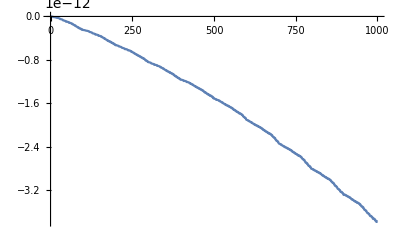
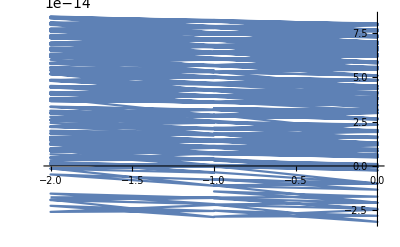
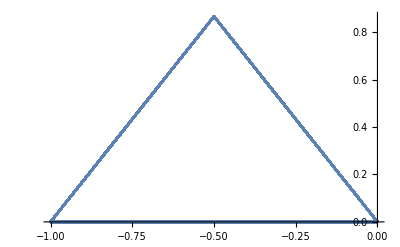
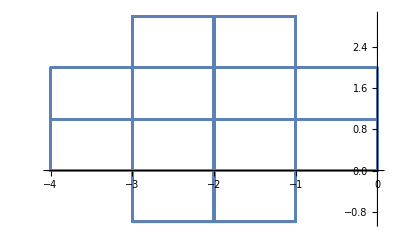
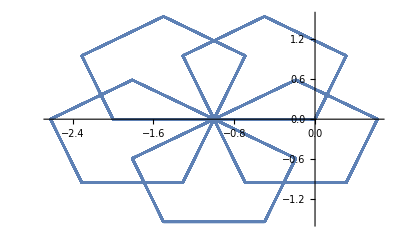
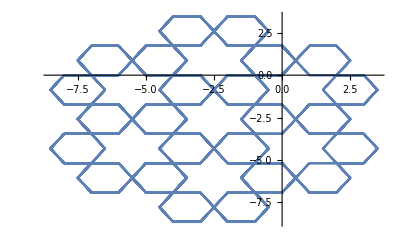
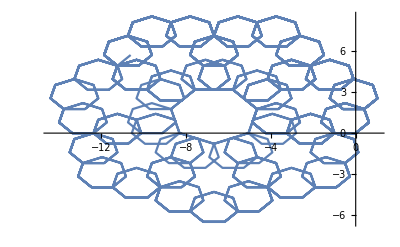
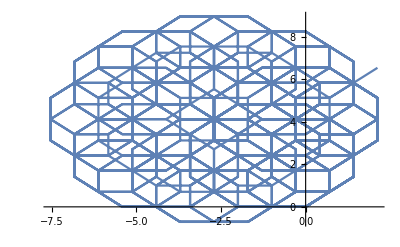
{{1,-Graphics-},{2,-Graphics-},{3,-Graphics-},{4,-Graphics-},{5,-Graphics-},{6,-Graphics-},{7,-Graphics-},{8,-Graphics-},{9,-Graphics-},{10,-Graphics-}}

```mathematica
Table[{k,ListLinePlot[(ReIm /@ expSumList[1000, 10, k])]}, {k, Range[10]}]
```

```mathematica
(* Table of some integer visualizations in base 10, varying by param n *)
```

```mathematica
Manipulate[list = ReIm /@ expSumList[10000, 2, 4];
maxRange = Max[Abs[list]];
ListLinePlot[Take[list,t],PlotRange->{{-maxRange, maxRange},{-maxRange, maxRange}}], {t, 1, 10000, 1}]
```

```mathematica
Manipulate[list = ReIm /@ expSumList[10000, 2, 1/Sqrt[3]];
partialList = Take[list, t];
maxRange = Max[Abs[partialList]]*1.1;
Graphics[Line[partialList], PlotRange->{{-maxRange, maxRange},{-maxRange, maxRange}}, Axes->True], {t, 2, 10000, 10}]
```

```mathematica
(* Table of some integer visualizations varying in base *)
```

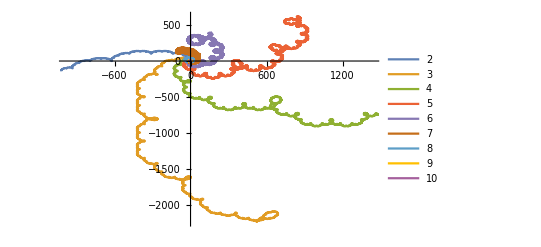

```mathematica
ListLinePlot[(ReIm /@ expSumList[10000, #, 10])& /@ Range[2,10], PlotLegends->Range[2,10]]
```

```mathematica
randomRealTable = RandomReal[{1,3}, 15]  (* 15 random real numbers ranging from 0 to 25 *)
```

{2.42147,2.57364,1.61802,1.40865,2.27935,1.66196,1.33148,1.26491,1.54759,1.88889,1.89473,1.68432,1.56827,2.59818,2.77027}

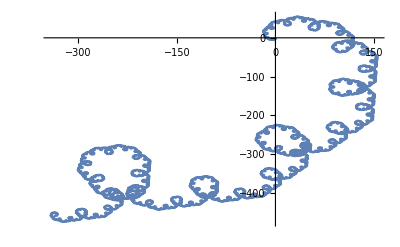
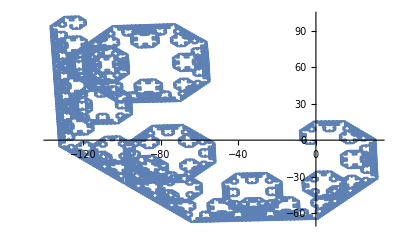
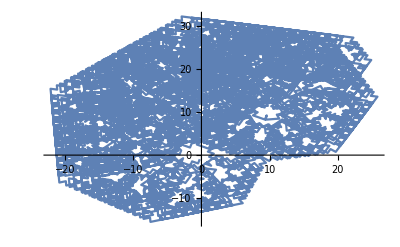
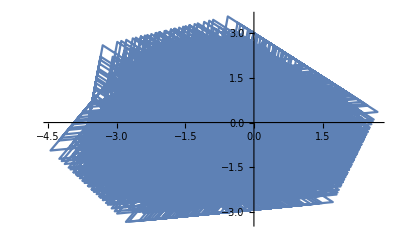
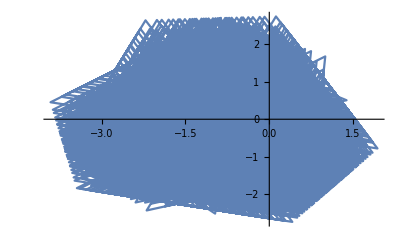
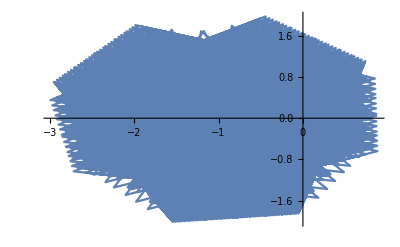
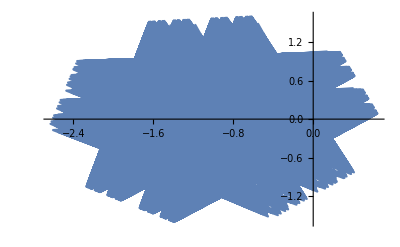
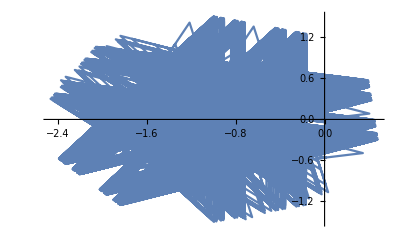
{{1.26491,-Graphics-},{1.33148,-Graphics-},{1.40865,-Graphics-},{1.54759,-Graphics-},{1.56827,-Graphics-},{1.61802,-Graphics-},{1.66196,-Graphics-},{1.68432,-Graphics-},{1.88889,-Graphics-},{1.89473,-Graphics-},{2.27935,-Graphics-},{2.42147,-Graphics-},{2.57364,-Graphics-},{2.59818,-Graphics-},{2.77027,-Graphics-}}

```mathematica
Sort[Table[{x, ListLinePlot[ReIm /@ expSumList[10000, 2, x]]}, {x, randomRealTable}]]
```

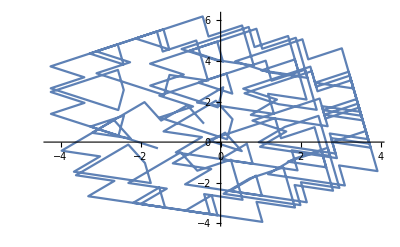

```mathematica
visualizer[250, 2, Pi]
```

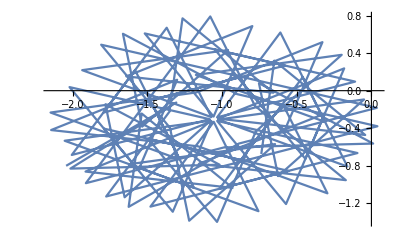

```mathematica
visualizer[100, 10, GoldenRatio]
```

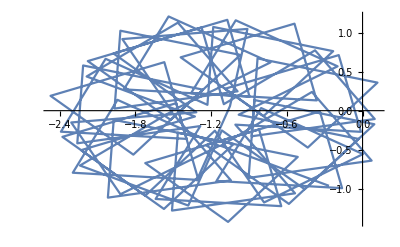

```mathematica
visualizer[100, 10, Sqrt[2]]
```

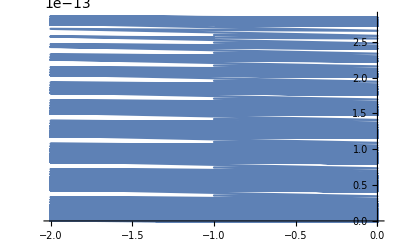
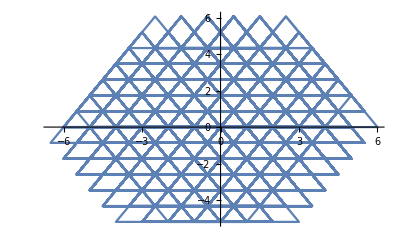
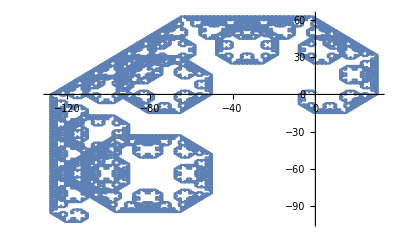
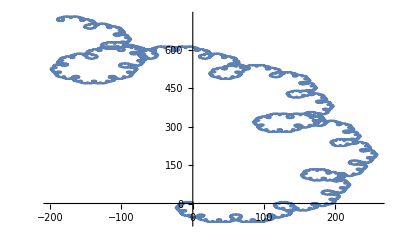
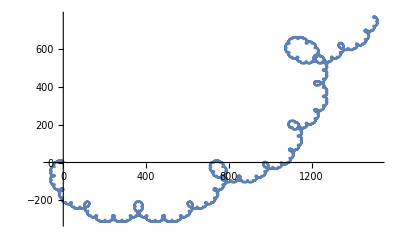
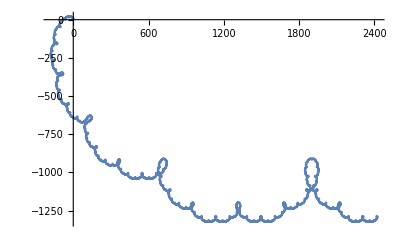
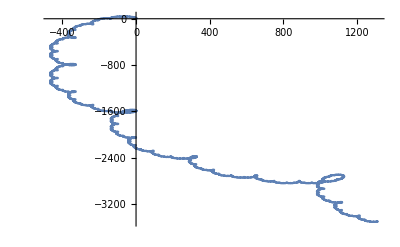
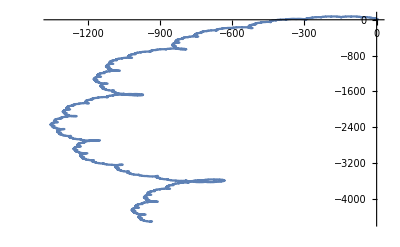
{{2,-Graphics-},{3,-Graphics-},{4,-Graphics-},{5,-Graphics-},{6,-Graphics-},{7,-Graphics-},{8,-Graphics-},{9,-Graphics-},{10,-Graphics-}}

```mathematica
Sort[Table[{x, ListLinePlot[ReIm /@ expSumList[10000, 2, x]]}, {x, Range[2,10]}]]
```

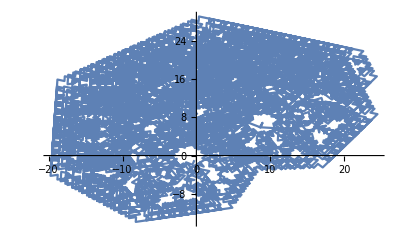
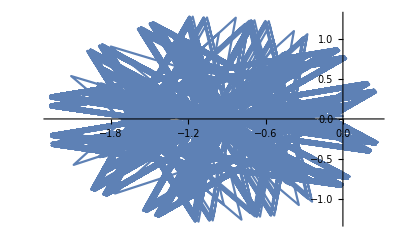
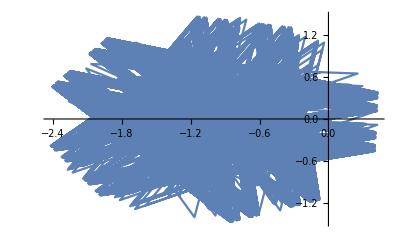
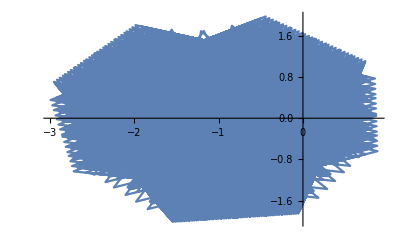
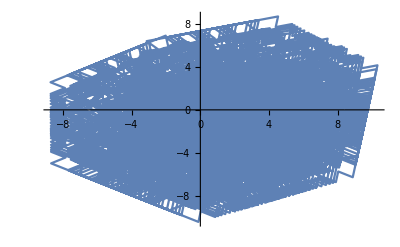
{{√2,-Graphics-},{√3,-Graphics-},{√6,-Graphics-},{GoldenRatio,-Graphics-},{π,-Graphics-}}

```mathematica
Sort[Table[{x, ListLinePlot[ReIm /@ expSumList[10000, 2, x]]}, {x, {Pi, GoldenRatio, Sqrt[2], Sqrt[3], Sqrt[6]}}]]
```

```mathematica
piTable = (#*Pi)& /@ Range[10]
```

{π,2 π,3 π,4 π,5 π,6 π,7 π,8 π,9 π,10 π}

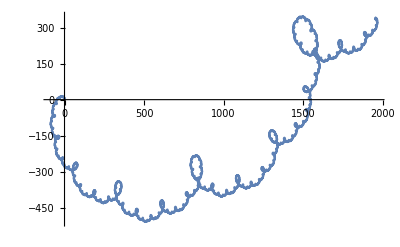
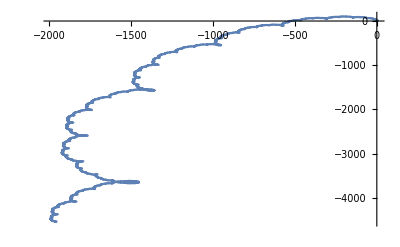
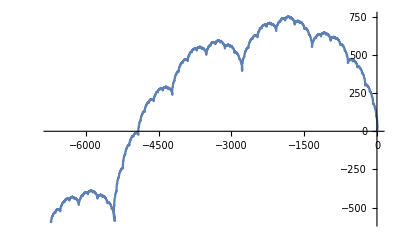
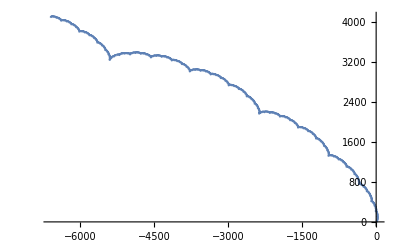
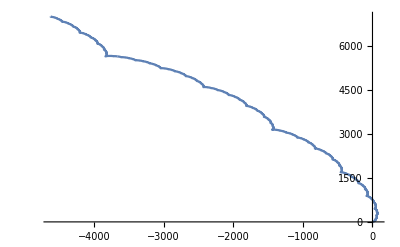
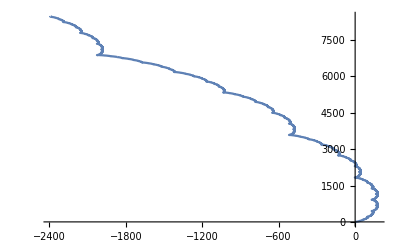
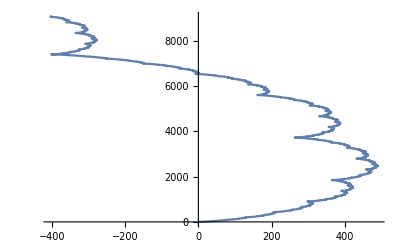
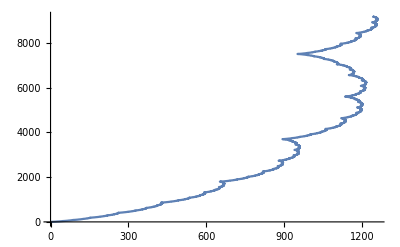
{{π,-Graphics-},{2 π,-Graphics-},{3 π,-Graphics-},{4 π,-Graphics-},{5 π,-Graphics-},{6 π,-Graphics-},{7 π,-Graphics-},{8 π,-Graphics-},{9 π,-Graphics-},{10 π,-Graphics-}}

```mathematica
Sort[Table[{x, ListLinePlot[ReIm /@ expSumList[10000, 2, x]]}, {x, piTable}]]
```